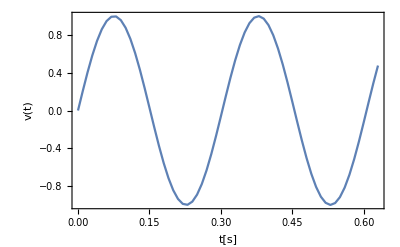

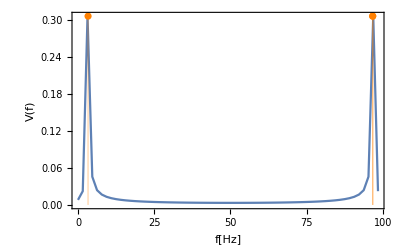

0.306181

0.306181

```mathematica
Clear["Global`*"]
Δt=.01; (*sampling interval = 1/sampling rate*)
n=2^6; (*number of sampling points*)
fmod=3.3;
t=Range[0,n-1]Δt;
v=Table[{tt,Sin[2π fmod tt]},{tt,t}];

(*define frequency domain; define rbw=Δf*)
rbw = 1/(n Δt);
f=Range[0,n-1]rbw;

(*normalized st PSDs have same total energy in t and f domain*)
Vnorm=√n Δt Fourier[v[[;;,2]]]; 

V=Thread[{f,Abs[Vnorm]}];

(*plot*)
ListPlot[v,Joined->True,Frame->True,Axes->False, FrameLabel->{"t[s]","v(t)","fmod="<>ToString[fmod]<>"Hz"},LabelStyle->Black]


Show[{ListPlot[V,Joined->True,PlotRange->All,Frame->True,Axes->False, FrameLabel->{"f[Hz]","V(f)","fmod="<>ToString[fmod]<>"Hz"},LabelStyle->Black],

ListPlot[{
{{fmod,Max[V[[;;,2]]]},
{n rbw-fmod,Max[V[[;;,2]]]}}
},PlotStyle->Orange,Filling->Axis]
}]

(*calculate total energy*)

Et = Total[Abs[v[[;;,2]]]^2]Δt
Ef = Total[Abs[V[[;;,2]]]^2]rbw
```